```mathematica
f[x_]:= 20Cos[x/30]ⅇ^(-x/100)+30
```

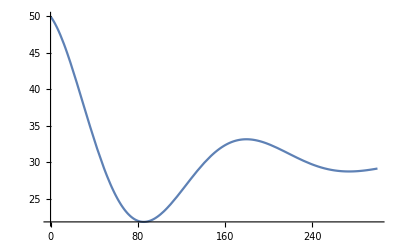

```mathematica
Plot[f[x],{x, 0, 300}]
```

```mathematica
g = 9.81
```

9.81

```mathematica
v[x_] = Sqrt[2g(f[0]-f[x])]
```

4.42945 √(7.5-7.5 ⅇ^(-x/100) Cos[x/30])

```mathematica
v[5]
```

```mathematica
3.019299473698834
v[1]
```

3.0193

1.24302

```mathematica
Show[Plot[f[x], {x,0,300}, PlotStyle->Red],
 Plot[v[x], {x,0,300}, PlotStyle->Green],PlotRange->All, AxesOrigin->{0,0}]
```

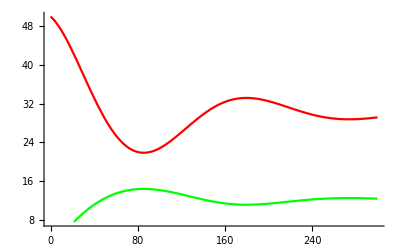

```mathematica
v[5]
```

3.0193

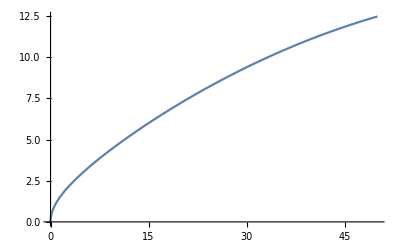

```mathematica
Plot[v[x], {x, 0, 50}]
```